```mathematica
Quit
```

```mathematica
Needs["LabQuest2`"]
```

```mathematica
labquest2=InstallLabQuest2["140.177.208.85"]
```

LabQuest2Object[…]

```mathematica
labquest2["Properties"]
```

{Status,Start,Stop,Sets,Set}

```mathematica
status=labquest2["Status"]
```

Dataset[<>]

```mathematica
sets=labquest2["Sets"]
```

Dataset[<>]

```mathematica
labquest2["Start"]
```

```mathematica
labquest2["Stop"]
```

```mathematica
data=labquest2[{"Set","279"}]
```

Data

Dataset[<>]

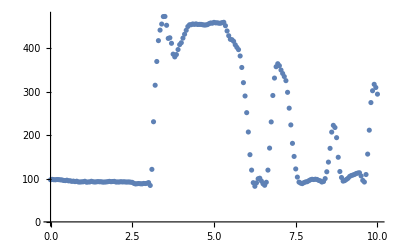

```mathematica
ListPlot@Transpose[Normal[data[All,"data"]]]
```